# Machine Reader 03

Flip Tanedo
12 February 2015
Based on Machine Reader 01 and 02

Updates:


Requires: PPPC Machine (version Feb 13+; please run entire notebook), data from PPPC Machine Runner. These were developed by FT and Jordan Smolinsky. All of this is based on PPPC4DMID by Marco Cirelli.

Remarks:
Feb 13: interpolated functions for on-shell mediators with threshold masses don’t work, e.g. degenerate DM and vector mediator (2-to-2).


Irrelevant Remarks: By the way, “PPPC Machine” was a reference to Gun Machine by Warren Ellis... which I thought was an okay novel. “PPPC Machine Runner” was a reference to Bit.Trip Runner by Gaijin Games. This notebook is a reference to Bernhard Schlink’s excellent novel, The Reader. 

Another interesting observation: now that I’m thinking about Gun Machine, I realized that one of the main plot devices ((a room full of guns mounted on the walls)) is a giant middle finger to the Chekov’s gun trope.

## Single Parameter Point Example

This is an example for how to read PPPC Machine outputs and do a simple analysis.

### Specifying source files

#### Directory in which output files are located

```mathematica
(*dirbb="/Users/fliptanedo/Documents/Work/PPPCMachineRunner/VVtobb/VV_b";*)
```

```mathematica
dirbb="/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b"
```

/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b

#### Parameters used

This is the range of DM masses and [vector] mediator masses used in part of our scane. VVtobbparams is a list of parameter points.

```mathematica
Vbmχrange=Range[15,300,3];
mχmVpairs[mχ_,min_,space_]:={mχ,#}&/@Range[min,mχ,space];
VVtobbparams=Flatten[mχmVpairs[#,15,3]&/@Vbmχrange,1];
Length[VVtobbparams]
```

4656

For simplicity we’ll only consider a small subset of these.

```mathematica
TestParams=VVtobbparams[[4600;;4603]]
```

{{300,132},{300,135},{300,138},{300,141}}

#### Sanity checks

Check that files exist for all of these parameters.

```mathematica
AllFilesExist[Filename[dirbb,#]&/@TestParams]
```

True

### Make some nice sanity check plots

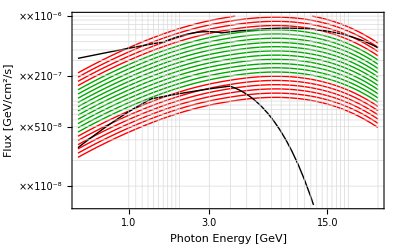

```mathematica
SuperPlot[
GetFunc[dirbb,TestParams[[1]]],
RangeOfNorms[
GetFunc[dirbb,TestParams[[1]]],
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
20],(* Number of divisions *)
MinEnv,MaxEnv,
2, (* Envelope Scaling *)
20, (* Number of energies to check *)
.5, (* min E *)
30] (* max E *)
```

### Output

```mathematica
FullTag["V","b",
dirbb,VVtobbparams[[4600]],
MinEnv,MaxEnv,
2,(* A *)
2, (* test energy *)
20, (* number of slices *)
20, (* number of energies to sample *)
1,50 (* minE and maxE *)
]
```

{V,b,{300,132},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_132.dat,{4.26228×10^-9,1.36924×10^-8},1.08}

Warnings: for the crappy parameter points, 30 energy samples seems to lead to problems. I don’t know why. I suggest 20-30 slices/20 energy samples. Otherwise one should do extensive tests and diagnose what’s causing the slowdown.

## VV case

### VV to bb, as a worked example with discussion

#### Directory in which output files are located

```mathematica
dirbb="/Users/fliptanedo/Documents/Work/PPPCMachineRunner/VVtobb/VV_b";
dirbb="/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b";
```

#### Parameters used

This is the range of DM masses and [vector] mediator masses used in part of our scane. VVtobbparams is a list of parameter points.

```mathematica
Vbmχrange=Range[15,300,3];
mχmVpairs[mχ_,min_,space_]:={mχ,#}&/@Range[min,mχ,space];
VVtobbparams=Flatten[mχmVpairs[#,15,3]&/@Vbmχrange,1];
Length[VVtobbparams]
```

4656

For simplicity we’ll only consider a small subset of these.

```mathematica
TestParams=VVtobbparams[[4600;;4603]]
```

{{300,132},{300,135},{300,138},{300,141}}

#### Removing the bad parameters

We need to remove the degenerate spectrum cases since these don’t give nice interpolating functions---they’re indeterminate everywhere.

```mathematica
Select[VVtobbparams[[1;;10]],#[[1]]!=#[[2]]&]
```

{{18,15},{21,15},{21,18},{24,15},{24,18},{24,21}}

```mathematica
GoodVVbbparams=Select[VVtobbparams,#[[1]]!=#[[2]]&];
Length[GoodVVbbparams]
```

4560

#### Check Files

```mathematica
AllFilesExist[Filename[dirbb,#]&/@GoodVVbbparams]
```

True

#### Generate outputs

```mathematica
Vbb01=FullTag["V","b",
dirbb,#,
MinEnv,MaxEnv,
2,(* A *)
2, (* test energy *)
20, (* number of slices *)
20, (* number of energies to sample *)
1,50 (* minE and maxE *)
]&/@GoodVVbbparams[[1;;1000]]//Timing
Vbb02=FullTag["V","b",
dirbb,#,
MinEnv,MaxEnv,
2,(* A *)
2, (* test energy *)
20, (* number of slices *)
20, (* number of energies to sample *)
1,50 (* minE and maxE *)
]&/@GoodVVbbparams[[1001;;2000]]//Timing
Vbb03=FullTag["V","b",
dirbb,#,
MinEnv,MaxEnv,
2,(* A *)
2, (* test energy *)
20, (* number of slices *)
20, (* number of energies to sample *)
1,50 (* minE and maxE *)
]&/@GoodVVbbparams[[2001;;3000]]//Timing
Vbb04=FullTag["V","b",
dirbb,#,
MinEnv,MaxEnv,
2,(* A *)
2, (* test energy *)
20, (* number of slices *)
20, (* number of energies to sample *)
1,50 (* minE and maxE *)
]&/@GoodVVbbparams[[3001;;4000]]//Timing
Vbb05=FullTag["V","b",
dirbb,#,
MinEnv,MaxEnv,
2,(* A *)
2, (* test energy *)
20, (* number of slices *)
20, (* number of energies to sample *)
1,50 (* minE and maxE *)
]&/@GoodVVbbparams[[4001;;Length[GoodVVbbparams]]]//Timing
```

{909.78987,{{V,b,{18,15},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_18_15.dat,{∞,-∞},10},«999»}}

{378.5149,{{V,b,{150,45},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_150_45.dat,{5.76296×10^-9,2.33803×10^-8},1.},«998»,{V,b,«3»,1.}}}

{694.04122,{{V,b,{204,156},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_204_156.dat,{4.52427×10^-9,1.69811×10^-8},1.},«998»,{V,«4»,1.04}}}

{1001.08641,{{V,b,{246,237},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_246_237.dat,{3.99178×10^-9,1.3861×10^-8},1.04},«998»,{«1»}}}

{673.32403,{{V,b,{282,267},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_282_267.dat,{4.04588×10^-9,1.29972×10^-8},1.07},{V,b,{282,270},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_282_270.dat,{4.04025×10^-9,1.29791×10^-8},1.06},{V,b,{282,273},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_282_273.dat,{4.03493×10^-9,1.2962×10^-8},1.06},{V,b,{282,276},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_282_276.dat,{4.02988×10^-9,1.29458×10^-8},1.06},{V,b,{282,279},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_282_279.dat,{4.02444×10^-9,1.29284×10^-8},1.06},{V,b,{285,15},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_15.dat,{4.28144×10^-9,1.3754×10^-8},1.07},{V,b,{285,18},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_18.dat,{4.34155×10^-9,1.39471×10^-8},1.07},{V,b,{285,21},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_21.dat,{4.38031×10^-9,1.40716×10^-8},1.07},{V,b,{285,24},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_24.dat,{4.40605×10^-9,1.41543×10^-8},1.08},{V,b,{285,27},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_27.dat,{4.42338×10^-9,1.42099×10^-8},1.08},{V,b,{285,30},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_30.dat,{4.43527×10^-9,1.42481×10^-8},1.08},{V,b,{285,33},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_33.dat,{4.44346×10^-9,1.42744×10^-8},1.08},{V,b,{285,36},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_36.dat,{4.44909×10^-9,1.42925×10^-8},1.08},{V,b,{285,39},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_39.dat,{4.45286×10^-9,1.43046×10^-8},1.08},{V,b,{285,42},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_42.dat,{4.45526×10^-9,1.43123×10^-8},1.08},{V,b,{285,45},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_45.dat,{4.45666×10^-9,1.43168×10^-8},1.08},{V,b,{285,48},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_48.dat,{4.45722×10^-9,1.43186×10^-8},1.08},{V,b,{285,51},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_51.dat,{4.4571×10^-9,1.43183×10^-8},1.08},{V,b,{285,54},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_54.dat,{4.45642×10^-9,1.43161×10^-8},1.08},{V,b,{285,57},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_57.dat,{4.45526×10^-9,1.43123×10^-8},1.08},{V,b,{285,60},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_60.dat,{4.45371×10^-9,1.43074×10^-8},1.08},{V,b,{285,63},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_63.dat,{4.45178×10^-9,1.43012×10^-8},1.08},{V,b,{285,66},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_66.dat,{4.4495×10^-9,1.42938×10^-8},1.08},{V,b,{285,69},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_69.dat,{4.44691×10^-9,1.42855×10^-8},1.08},{V,b,{285,72},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_72.dat,{4.44401×10^-9,1.42762×10^-8},1.08},{V,b,{285,75},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_75.dat,{4.44085×10^-9,1.42661×10^-8},1.08},{V,b,{285,78},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_78.dat,{4.43744×10^-9,1.42551×10^-8},1.08},{V,b,{285,81},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_81.dat,{4.43376×10^-9,1.42433×10^-8},1.08},{V,b,{285,84},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_84.dat,{4.42987×10^-9,1.42308×10^-8},1.08},{V,b,{285,87},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_87.dat,{4.42577×10^-9,1.42176×10^-8},1.08},{V,b,{285,90},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_90.dat,{4.42146×10^-9,1.42038×10^-8},1.08},{V,b,{285,93},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_93.dat,{4.41698×10^-9,1.41894×10^-8},1.08},{V,b,{285,96},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_96.dat,{4.41219×10^-9,1.4174×10^-8},1.08},{V,b,{285,99},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_99.dat,{4.40731×10^-9,1.41583×10^-8},1.08},{V,b,{285,102},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_102.dat,{4.4022×10^-9,1.41419×10^-8},1.08},{V,b,{285,105},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_105.dat,{4.39697×10^-9,1.41251×10^-8},1.08},{V,b,{285,108},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_108.dat,{4.39155×10^-9,1.41077×10^-8},1.08},{V,b,{285,111},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_111.dat,{4.38599×10^-9,1.40898×10^-8},1.08},{V,b,{285,114},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_114.dat,{4.38031×10^-9,1.40716×10^-8},1.07},{V,b,{285,117},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_117.dat,{4.37455×10^-9,1.40531×10^-8},1.07},{V,b,{285,120},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_120.dat,{4.36867×10^-9,1.40342×10^-8},1.07},{V,b,{285,123},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_123.dat,{4.36259×10^-9,1.40147×10^-8},1.07},{V,b,{285,126},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_126.dat,{4.35638×10^-9,1.39947×10^-8},1.07},{V,b,{285,129},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_129.dat,{4.35004×10^-9,1.39743×10^-8},1.07},{V,b,{285,132},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_132.dat,{4.34371×10^-9,1.3954×10^-8},1.07},{V,b,{285,135},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_135.dat,{4.33721×10^-9,1.39331×10^-8},1.07},{V,b,{285,138},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_138.dat,{4.33061×10^-9,1.39119×10^-8},1.07},{V,b,{285,141},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_141.dat,{4.32383×10^-9,1.38901×10^-8},1.07},{V,b,{285,144},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_144.dat,{4.31714×10^-9,1.38686×10^-8},1.07},{V,b,{285,147},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_147.dat,{4.31047×10^-9,1.38472×10^-8},1.07},{V,b,{285,150},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_150.dat,{4.3037×10^-9,1.38255×10^-8},1.07},{V,b,{285,153},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_153.dat,{4.29681×10^-9,1.38033×10^-8},1.07},{V,b,{285,156},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_156.dat,{4.28987×10^-9,1.3781×10^-8},1.07},{V,b,{285,159},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_159.dat,{4.28287×10^-9,1.37585×10^-8},1.07},{V,b,{285,162},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_162.dat,{4.27574×10^-9,1.37356×10^-8},1.07},{V,b,{285,165},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_165.dat,{4.26859×10^-9,1.37127×10^-8},1.07},{V,b,{285,168},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_168.dat,{4.26146×10^-9,1.36898×10^-8},1.07},{V,b,{285,171},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_171.dat,{4.25441×10^-9,1.36671×10^-8},1.07},{V,b,{285,174},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_174.dat,{4.24725×10^-9,1.36441×10^-8},1.07},{V,b,{285,177},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_177.dat,{4.24009×10^-9,1.36211×10^-8},1.07},{V,b,{285,180},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_180.dat,{4.2328×10^-9,1.35977×10^-8},1.07},{V,b,{285,183},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_183.dat,{4.22556×10^-9,1.35744×10^-8},1.07},{V,b,{285,186},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_186.dat,{4.21836×10^-9,1.35513×10^-8},1.07},{V,b,{285,189},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_189.dat,{4.21103×10^-9,1.35278×10^-8},1.07},{V,b,{285,192},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_192.dat,{4.20362×10^-9,1.3504×10^-8},1.07},{V,b,{285,195},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_195.dat,{4.19609×10^-9,1.34798×10^-8},1.07},{V,b,{285,198},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_198.dat,{4.18873×10^-9,1.34561×10^-8},1.07},{V,b,{285,201},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_201.dat,{4.18148×10^-9,1.34328×10^-8},1.07},{V,b,{285,204},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_204.dat,{4.17435×10^-9,1.34099×10^-8},1.07},{V,b,{285,207},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_207.dat,{4.16722×10^-9,1.3387×10^-8},1.07},{V,b,{285,210},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_210.dat,{4.16005×10^-9,1.3364×10^-8},1.07},{V,b,{285,213},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_213.dat,{4.15282×10^-9,1.33408×10^-8},1.07},{V,b,{285,216},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_216.dat,{4.14561×10^-9,1.33176×10^-8},1.07},{V,b,{285,219},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_219.dat,{4.13832×10^-9,1.32942×10^-8},1.07},{V,b,{285,222},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_222.dat,{4.13101×10^-9,1.32707×10^-8},1.07},{V,b,{285,225},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_225.dat,{4.12415×10^-9,1.32487×10^-8},1.07},{V,b,{285,228},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_228.dat,{4.11721×10^-9,1.32264×10^-8},1.07},{V,b,{285,231},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_231.dat,{4.11028×10^-9,1.32041×10^-8},1.07},{V,b,{285,234},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_234.dat,{4.10326×10^-9,1.31816×10^-8},1.07},{V,b,{285,237},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_237.dat,{4.09633×10^-9,1.31593×10^-8},1.07},{V,b,{285,240},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_240.dat,{4.08949×10^-9,1.31373×10^-8},1.07},{V,b,{285,243},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_243.dat,{4.08273×10^-9,1.31156×10^-8},1.07},{V,b,{285,246},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_246.dat,{4.07605×10^-9,1.30942×10^-8},1.07},{V,b,{285,249},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_249.dat,{4.06932×10^-9,1.30725×10^-8},1.07},{V,b,{285,252},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_252.dat,{4.06273×10^-9,1.30514×10^-8},1.07},{V,b,{285,255},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_255.dat,{4.05631×10^-9,1.30307×10^-8},1.07},{V,b,{285,258},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_258.dat,{4.04992×10^-9,1.30102×10^-8},1.07},{V,b,{285,261},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_261.dat,{4.04358×10^-9,1.29898×10^-8},1.07},{V,b,{285,264},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_264.dat,{4.03769×10^-9,1.29709×10^-8},1.07},{V,b,{285,267},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_267.dat,{4.03163×10^-9,1.29514×10^-8},1.07},{V,b,{285,270},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_270.dat,{4.02575×10^-9,1.29325×10^-8},1.07},{V,b,{285,273},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_273.dat,{4.02008×10^-9,1.29144×10^-8},1.07},{V,b,{285,276},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_276.dat,{4.01448×10^-9,1.28963×10^-8},1.07},{V,b,{285,279},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_279.dat,{4.0092×10^-9,1.28794×10^-8},1.07},{V,b,{285,282},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_285_282.dat,{4.00339×10^-9,1.28607×10^-8},1.07},{V,b,{288,15},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_15.dat,{4.26158×10^-9,1.36901×10^-8},1.07},{V,b,{288,18},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_18.dat,{4.32155×10^-9,1.38828×10^-8},1.07},{V,b,{288,21},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_21.dat,{4.36042×10^-9,1.40077×10^-8},1.08},{V,b,{288,24},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_24.dat,{4.38611×10^-9,1.40902×10^-8},1.08},{V,b,{288,27},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_27.dat,{4.40345×10^-9,1.41459×10^-8},1.08},{V,b,{288,30},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_30.dat,{4.41531×10^-9,1.4184×10^-8},1.08},{V,b,{288,33},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_33.dat,{4.4235×10^-9,1.42103×10^-8},1.08},{V,b,{288,36},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_36.dat,{4.42921×10^-9,1.42287×10^-8},1.08},{V,b,{288,39},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_39.dat,{4.43305×10^-9,1.4241×10^-8},1.08},{V,b,{288,42},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_42.dat,{4.43551×10^-9,1.42489×10^-8},1.08},{V,b,{288,45},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_45.dat,{4.43693×10^-9,1.42535×10^-8},1.08},{V,b,{288,48},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_48.dat,{4.43753×10^-9,1.42554×10^-8},1.08},{V,b,{288,51},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_51.dat,{4.43747×10^-9,1.42552×10^-8},1.08},{V,b,{288,54},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_54.dat,{4.43686×10^-9,1.42532×10^-8},1.08},{V,b,{288,57},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_57.dat,{4.43578×10^-9,1.42498×10^-8},1.08},{V,b,{288,60},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_60.dat,{4.43428×10^-9,1.42449×10^-8},1.08},{V,b,{288,63},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_63.dat,{4.43241×10^-9,1.42389×10^-8},1.08},{V,b,{288,66},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_66.dat,{4.43019×10^-9,1.42318×10^-8},1.08},{V,b,{288,69},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_69.dat,{4.42766×10^-9,1.42237×10^-8},1.08},{V,b,{288,72},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_72.dat,{4.42483×10^-9,1.42146×10^-8},1.08},{V,b,{288,75},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_75.dat,{4.42175×10^-9,1.42047×10^-8},1.08},{V,b,{288,78},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_78.dat,{4.41844×10^-9,1.41941×10^-8},1.08},{V,b,{288,81},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_81.dat,{4.41487×10^-9,1.41826×10^-8},1.08},{V,b,{288,84},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_84.dat,{4.4111×10^-9,1.41705×10^-8},1.08},{V,b,{288,87},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_87.dat,{4.40709×10^-9,1.41576×10^-8},1.08},{V,b,{288,90},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_90.dat,{4.40288×10^-9,1.41441×10^-8},1.08},{V,b,{288,93},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_93.dat,{4.39849×10^-9,1.413×10^-8},1.08},{V,b,{288,96},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_96.dat,{4.39386×10^-9,1.41151×10^-8},1.08},{V,b,{288,99},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_99.dat,{4.38909×10^-9,1.40998×10^-8},1.08},{V,b,{288,102},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_102.dat,{4.38407×10^-9,1.40837×10^-8},1.08},{V,b,{288,105},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_105.dat,{4.37894×10^-9,1.40672×10^-8},1.08},{V,b,{288,108},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_108.dat,{4.37365×10^-9,1.40502×10^-8},1.08},{V,b,{288,111},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_111.dat,{4.36826×10^-9,1.40328×10^-8},1.08},{V,b,{288,114},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_114.dat,{4.36271×10^-9,1.4015×10^-8},1.08},{V,b,{288,117},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_117.dat,{4.35702×10^-9,1.39967×10^-8},1.08},{V,b,{288,120},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_120.dat,{4.35123×10^-9,1.39781×10^-8},1.08},{V,b,{288,123},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_123.dat,{4.34528×10^-9,1.3959×10^-8},1.08},{V,b,{288,126},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_126.dat,{4.33919×10^-9,1.39395×10^-8},1.08},{V,b,{288,129},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_129.dat,{4.33293×10^-9,1.39194×10^-8},1.08},{V,b,{288,132},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_132.dat,{4.32667×10^-9,1.38993×10^-8},1.07},{V,b,{288,135},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_135.dat,{4.32026×10^-9,1.38787×10^-8},1.07},{V,b,{288,138},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_138.dat,{4.31373×10^-9,1.38577×10^-8},1.07},{V,b,{288,141},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_141.dat,{4.30708×10^-9,1.38363×10^-8},1.07},{V,b,{288,144},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_144.dat,{4.30051×10^-9,1.38152×10^-8},1.07},{V,b,{288,147},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_147.dat,{4.29397×10^-9,1.37942×10^-8},1.07},{V,b,{288,150},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_150.dat,{4.28734×10^-9,1.37729×10^-8},1.07},{V,b,{288,153},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_153.dat,{4.28056×10^-9,1.37511×10^-8},1.07},{V,b,{288,156},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_156.dat,{4.27369×10^-9,1.37291×10^-8},1.07},{V,b,{288,159},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_159.dat,{4.26684×10^-9,1.37071×10^-8},1.07},{V,b,{288,162},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_162.dat,{4.25989×10^-9,1.36847×10^-8},1.07},{V,b,{288,165},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_165.dat,{4.25291×10^-9,1.36623×10^-8},1.07},{V,b,{288,168},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_168.dat,{4.24589×10^-9,1.36398×10^-8},1.07},{V,b,{288,171},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_171.dat,{4.23894×10^-9,1.36174×10^-8},1.07},{V,b,{288,174},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_174.dat,{4.23191×10^-9,1.35948×10^-8},1.07},{V,b,{288,177},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_177.dat,{4.22482×10^-9,1.35721×10^-8},1.07},{V,b,{288,180},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_180.dat,{4.21771×10^-9,1.35492×10^-8},1.07},{V,b,{288,183},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_183.dat,{4.21059×10^-9,1.35264×10^-8},1.07},{V,b,{288,186},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_186.dat,{4.20352×10^-9,1.35036×10^-8},1.07},{V,b,{288,189},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_189.dat,{4.19633×10^-9,1.34805×10^-8},1.07},{V,b,{288,192},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_192.dat,{4.1891×10^-9,1.34573×10^-8},1.07},{V,b,{288,195},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_195.dat,{4.18172×10^-9,1.34336×10^-8},1.07},{V,b,{288,198},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_198.dat,{4.17447×10^-9,1.34103×10^-8},1.07},{V,b,{288,201},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_201.dat,{4.16731×10^-9,1.33873×10^-8},1.07},{V,b,{288,204},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_204.dat,{4.16015×10^-9,1.33643×10^-8},1.07},{V,b,{288,207},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_207.dat,{4.15311×10^-9,1.33417×10^-8},1.07},{V,b,{288,210},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_210.dat,{4.14604×10^-9,1.3319×10^-8},1.07},{V,b,{288,213},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_213.dat,{4.13898×10^-9,1.32963×10^-8},1.07},{V,b,{288,216},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_216.dat,{4.1319×10^-9,1.32736×10^-8},1.07},{V,b,{288,219},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_219.dat,{4.1248×10^-9,1.32508×10^-8},1.07},{V,b,{288,222},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_222.dat,{4.11757×10^-9,1.32275×10^-8},1.07},{V,b,{288,225},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_225.dat,{4.11065×10^-9,1.32053×10^-8},1.07},{V,b,{288,228},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_228.dat,{4.10377×10^-9,1.31832×10^-8},1.07},{V,b,{288,231},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_231.dat,{4.09679×10^-9,1.31608×10^-8},1.07},{V,b,{288,234},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_234.dat,{4.0899×10^-9,1.31386×10^-8},1.07},{V,b,{288,237},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_237.dat,{4.08298×10^-9,1.31164×10^-8},1.07},{V,b,{288,240},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_240.dat,{4.07623×10^-9,1.30947×10^-8},1.07},{V,b,{288,243},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_243.dat,{4.06953×10^-9,1.30732×10^-8},1.07},{V,b,{288,246},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_246.dat,{4.06284×10^-9,1.30517×10^-8},1.07},{V,b,{288,249},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_249.dat,{4.05624×10^-9,1.30305×10^-8},1.07},{V,b,{288,252},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_252.dat,{4.0497×10^-9,1.30095×10^-8},1.07},{V,b,{288,255},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_255.dat,{4.04297×10^-9,1.29879×10^-8},1.07},{V,b,{288,258},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_258.dat,{4.03672×10^-9,1.29678×10^-8},1.07},{V,b,{288,261},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_261.dat,{4.03038×10^-9,1.29474×10^-8},1.08},{V,b,{288,264},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_264.dat,{4.02406×10^-9,1.29271×10^-8},1.07},{V,b,{288,267},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_267.dat,{4.01798×10^-9,1.29076×10^-8},1.07},{V,b,{288,270},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_270.dat,{4.01199×10^-9,1.28883×10^-8},1.07},{V,b,{288,273},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_273.dat,{4.00598×10^-9,1.2869×10^-8},1.07},{V,b,{288,276},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_276.dat,{4.00028×10^-9,1.28508×10^-8},1.07},{V,b,{288,279},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_279.dat,{3.99451×10^-9,1.28322×10^-8},1.07},{V,b,{288,282},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_282.dat,{3.98879×10^-9,1.28138×10^-8},1.07},{V,b,{288,285},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_288_285.dat,{3.98275×10^-9,1.27944×10^-8},1.07},{V,b,{291,15},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_15.dat,{4.24229×10^-9,1.36282×10^-8},1.07},{V,b,{291,18},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_18.dat,{4.30218×10^-9,1.38206×10^-8},1.08},{V,b,{291,21},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_21.dat,{4.341×10^-9,1.39453×10^-8},1.08},{V,b,{291,24},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_24.dat,{4.36648×10^-9,1.40271×10^-8},1.08},{V,b,{291,27},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_27.dat,{4.38389×10^-9,1.40831×10^-8},1.08},{V,b,{291,30},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_30.dat,{4.39582×10^-9,1.41214×10^-8},1.08},{V,b,{291,33},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_33.dat,{4.40406×10^-9,1.41479×10^-8},1.08},{V,b,{291,36},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_36.dat,{4.40983×10^-9,1.41664×10^-8},1.08},{V,b,{291,39},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_39.dat,{4.41371×10^-9,1.41789×10^-8},1.08},{V,b,{291,42},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_42.dat,{4.41622×10^-9,1.41869×10^-8},1.08},{V,b,{291,45},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_45.dat,{4.4177×10^-9,1.41917×10^-8},1.08},{V,b,{291,48},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_48.dat,{4.41835×10^-9,1.41938×10^-8},1.08},{V,b,{291,51},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_51.dat,{4.41834×10^-9,1.41937×10^-8},1.08},{V,b,{291,54},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_54.dat,{4.41778×10^-9,1.4192×10^-8},1.08},{V,b,{291,57},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_57.dat,{4.41675×10^-9,1.41886×10^-8},1.08},{V,b,{291,60},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_60.dat,{4.41531×10^-9,1.4184×10^-8},1.08},{V,b,{291,63},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_63.dat,{4.4135×10^-9,1.41782×10^-8},1.08},{V,b,{291,66},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_66.dat,{4.41135×10^-9,1.41713×10^-8},1.08},{V,b,{291,69},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_69.dat,{4.40889×10^-9,1.41634×10^-8},1.08},{V,b,{291,72},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_72.dat,{4.40612×10^-9,1.41545×10^-8},1.08},{V,b,{291,75},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_75.dat,{4.40311×10^-9,1.41448×10^-8},1.08},{V,b,{291,78},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_78.dat,{4.39986×10^-9,1.41344×10^-8},1.08},{V,b,{291,81},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_81.dat,{4.3964×10^-9,1.41233×10^-8},1.08},{V,b,{291,84},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_84.dat,{4.3927×10^-9,1.41114×10^-8},1.08},{V,b,{291,87},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_87.dat,{4.38876×10^-9,1.40987×10^-8},1.08},{V,b,{291,90},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_90.dat,{4.38464×10^-9,1.40855×10^-8},1.08},{V,b,{291,93},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_93.dat,{4.38034×10^-9,1.40717×10^-8},1.08},{V,b,{291,96},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_96.dat,{4.37584×10^-9,1.40572×10^-8},1.08},{V,b,{291,99},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_99.dat,{4.37116×10^-9,1.40422×10^-8},1.08},{V,b,{291,102},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_102.dat,{4.36623×10^-9,1.40263×10^-8},1.08},{V,b,{291,105},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_105.dat,{4.36125×10^-9,1.40103×10^-8},1.08},{V,b,{291,108},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_108.dat,{4.35615×10^-9,1.3994×10^-8},1.08},{V,b,{291,111},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_111.dat,{4.3509×10^-9,1.39771×10^-8},1.08},{V,b,{291,114},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_114.dat,{4.34547×10^-9,1.39597×10^-8},1.08},{V,b,{291,117},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_117.dat,{4.3399×10^-9,1.39417×10^-8},1.08},{V,b,{291,120},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_120.dat,{4.33422×10^-9,1.39235×10^-8},1.08},{V,b,{291,123},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_123.dat,{4.32841×10^-9,1.39048×10^-8},1.08},{V,b,{291,126},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_126.dat,{4.32244×10^-9,1.38857×10^-8},1.08},{V,b,{291,129},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_129.dat,{4.31627×10^-9,1.38658×10^-8},1.08},{V,b,{291,132},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_132.dat,{4.31014×10^-9,1.38462×10^-8},1.08},{V,b,{291,135},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_135.dat,{4.30388×10^-9,1.3826×10^-8},1.08},{V,b,{291,138},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_138.dat,{4.29752×10^-9,1.38056×10^-8},1.08},{V,b,{291,141},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_141.dat,{4.29101×10^-9,1.37847×10^-8},1.08},{V,b,{291,144},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_144.dat,{4.28457×10^-9,1.3764×10^-8},1.08},{V,b,{291,147},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_147.dat,{4.27816×10^-9,1.37434×10^-8},1.08},{V,b,{291,150},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_150.dat,{4.27161×10^-9,1.37224×10^-8},1.08},{V,b,{291,153},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_153.dat,{4.2649×10^-9,1.37008×10^-8},1.07},{V,b,{291,156},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_156.dat,{4.25808×10^-9,1.36789×10^-8},1.07},{V,b,{291,159},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_159.dat,{4.25139×10^-9,1.36574×10^-8},1.07},{V,b,{291,162},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_162.dat,{4.24452×10^-9,1.36353×10^-8},1.07},{V,b,{291,165},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_165.dat,{4.23757×10^-9,1.3613×10^-8},1.07},{V,b,{291,168},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_168.dat,{4.23064×10^-9,1.35908×10^-8},1.07},{V,b,{291,171},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_171.dat,{4.22374×10^-9,1.35686×10^-8},1.07},{V,b,{291,174},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_174.dat,{4.21685×10^-9,1.35464×10^-8},1.07},{V,b,{291,177},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_177.dat,{4.20989×10^-9,1.35241×10^-8},1.07},{V,b,{291,180},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_180.dat,{4.2029×10^-9,1.35016×10^-8},1.07},{V,b,{291,183},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_183.dat,{4.19578×10^-9,1.34788×10^-8},1.07},{V,b,{291,186},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_186.dat,{4.1888×10^-9,1.34563×10^-8},1.07},{V,b,{291,189},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_189.dat,{4.1818×10^-9,1.34339×10^-8},1.07},{V,b,{291,192},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_192.dat,{4.17469×10^-9,1.3411×10^-8},1.07},{V,b,{291,195},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_195.dat,{4.16746×10^-9,1.33878×10^-8},1.07},{V,b,{291,198},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_198.dat,{4.1603×10^-9,1.33648×10^-8},1.07},{V,b,{291,201},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_201.dat,{4.15337×10^-9,1.33425×10^-8},1.07},{V,b,{291,204},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_204.dat,{4.14636×10^-9,1.332×10^-8},1.07},{V,b,{291,207},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_207.dat,{4.13942×10^-9,1.32977×10^-8},1.07},{V,b,{291,210},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_210.dat,{4.13236×10^-9,1.3275×10^-8},1.07},{V,b,{291,213},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_213.dat,{4.12531×10^-9,1.32524×10^-8},1.07},{V,b,{291,216},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_216.dat,{4.11835×10^-9,1.323×10^-8},1.07},{V,b,{291,219},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_219.dat,{4.11139×10^-9,1.32077×10^-8},1.07},{V,b,{291,222},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_222.dat,{4.10431×10^-9,1.31849×10^-8},1.07},{V,b,{291,225},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_225.dat,{4.09734×10^-9,1.31625×10^-8},1.07},{V,b,{291,228},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_228.dat,{4.09062×10^-9,1.3141×10^-8},1.07},{V,b,{291,231},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_231.dat,{4.08378×10^-9,1.3119×10^-8},1.07},{V,b,{291,234},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_234.dat,{4.07694×10^-9,1.3097×10^-8},1.07},{V,b,{291,237},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_237.dat,{4.07×10^-9,1.30747×10^-8},1.07},{V,b,{291,240},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_240.dat,{4.06315×10^-9,1.30527×10^-8},1.07},{V,b,{291,243},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_243.dat,{4.05657×10^-9,1.30316×10^-8},1.08},{V,b,{291,246},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_246.dat,{4.04997×10^-9,1.30104×10^-8},1.08},{V,b,{291,249},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_249.dat,{4.04338×10^-9,1.29892×10^-8},1.08},{V,b,{291,252},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_252.dat,{4.03675×10^-9,1.29679×10^-8},1.08},{V,b,{291,255},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_255.dat,{4.03025×10^-9,1.2947×10^-8},1.08},{V,b,{291,258},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_258.dat,{4.02386×10^-9,1.29265×10^-8},1.08},{V,b,{291,261},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_261.dat,{4.01745×10^-9,1.29059×10^-8},1.08},{V,b,{291,264},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_264.dat,{4.01104×10^-9,1.28853×10^-8},1.08},{V,b,{291,267},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_267.dat,{4.00497×10^-9,1.28658×10^-8},1.08},{V,b,{291,270},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_270.dat,{3.9988×10^-9,1.2846×10^-8},1.08},{V,b,{291,273},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_273.dat,{3.99277×10^-9,1.28266×10^-8},1.08},{V,b,{291,276},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_276.dat,{3.98683×10^-9,1.28075×10^-8},1.08},{V,b,{291,279},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_279.dat,{3.98088×10^-9,1.27884×10^-8},1.08},{V,b,{291,282},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_282.dat,{3.9749×10^-9,1.27692×10^-8},1.08},{V,b,{291,285},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_285.dat,{3.96882×10^-9,1.27497×10^-8},1.08},{V,b,{291,288},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_291_288.dat,{3.96255×10^-9,1.27295×10^-8},1.08},{V,b,{294,15},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_15.dat,{4.22362×10^-9,1.35682×10^-8},1.08},{V,b,{294,18},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_18.dat,{4.28338×10^-9,1.37602×10^-8},1.08},{V,b,{294,21},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_21.dat,{4.3219×10^-9,1.38839×10^-8},1.08},{V,b,{294,24},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_24.dat,{4.34733×10^-9,1.39656×10^-8},1.08},{V,b,{294,27},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_27.dat,{4.36468×10^-9,1.40214×10^-8},1.08},{V,b,{294,30},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_30.dat,{4.37666×10^-9,1.40599×10^-8},1.08},{V,b,{294,33},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_33.dat,{4.38492×10^-9,1.40864×10^-8},1.08},{V,b,{294,36},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_36.dat,{4.39072×10^-9,1.4105×10^-8},1.08},{V,b,{294,39},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_39.dat,{4.39466×10^-9,1.41177×10^-8},1.08},{V,b,{294,42},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_42.dat,{4.39724×10^-9,1.4126×10^-8},1.08},{V,b,{294,45},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_45.dat,{4.39876×10^-9,1.41308×10^-8},1.08},{V,b,{294,48},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_48.dat,{4.39946×10^-9,1.41331×10^-8},1.08},{V,b,{294,51},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_51.dat,{4.3995×10^-9,1.41332×10^-8},1.08},{V,b,{294,54},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_54.dat,{4.399×10^-9,1.41316×10^-8},1.08},{V,b,{294,57},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_57.dat,{4.39803×10^-9,1.41285×10^-8},1.08},{V,b,{294,60},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_60.dat,{4.39663×10^-9,1.4124×10^-8},1.08},{V,b,{294,63},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_63.dat,{4.39487×10^-9,1.41183×10^-8},1.08},{V,b,{294,66},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_66.dat,{4.39278×10^-9,1.41116×10^-8},1.08},{V,b,{294,69},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_69.dat,{4.39038×10^-9,1.41039×10^-8},1.08},{V,b,{294,72},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_72.dat,{4.38767×10^-9,1.40952×10^-8},1.08},{V,b,{294,75},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_75.dat,{4.38475×10^-9,1.40858×10^-8},1.08},{V,b,{294,78},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_78.dat,{4.38161×10^-9,1.40758×10^-8},1.08},{V,b,{294,81},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_81.dat,{4.37823×10^-9,1.40649×10^-8},1.08},{V,b,{294,84},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_84.dat,{4.37461×10^-9,1.40533×10^-8},1.08},{V,b,{294,87},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_87.dat,{4.37076×10^-9,1.40409×10^-8},1.08},{V,b,{294,90},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_90.dat,{4.36671×10^-9,1.40279×10^-8},1.08},{V,b,{294,93},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_93.dat,{4.36252×10^-9,1.40144×10^-8},1.08},{V,b,{294,96},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_96.dat,{4.35812×10^-9,1.40003×10^-8},1.08},{V,b,{294,99},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_99.dat,{4.35352×10^-9,1.39855×10^-8},1.08},{V,b,{294,102},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_102.dat,{4.34878×10^-9,1.39703×10^-8},1.08},{V,b,{294,105},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_105.dat,{4.34396×10^-9,1.39548×10^-8},1.08},{V,b,{294,108},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_108.dat,{4.33896×10^-9,1.39387×10^-8},1.08},{V,b,{294,111},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_111.dat,{4.33381×10^-9,1.39222×10^-8},1.08},{V,b,{294,114},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_114.dat,{4.32849×10^-9,1.39051×10^-8},1.08},{V,b,{294,117},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_117.dat,{4.323×10^-9,1.38875×10^-8},1.08},{V,b,{294,120},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_120.dat,{4.31748×10^-9,1.38697×10^-8},1.08},{V,b,{294,123},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_123.dat,{4.31181×10^-9,1.38515×10^-8},1.08},{V,b,{294,126},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_126.dat,{4.30602×10^-9,1.38329×10^-8},1.08},{V,b,{294,129},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_129.dat,{4.30004×10^-9,1.38137×10^-8},1.08},{V,b,{294,132},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_132.dat,{4.29404×10^-9,1.37944×10^-8},1.08},{V,b,{294,135},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_135.dat,{4.28795×10^-9,1.37749×10^-8},1.08},{V,b,{294,138},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_138.dat,{4.28171×10^-9,1.37548×10^-8},1.08},{V,b,{294,141},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_141.dat,{4.2754×10^-9,1.37345×10^-8},1.08},{V,b,{294,144},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_144.dat,{4.26907×10^-9,1.37142×10^-8},1.08},{V,b,{294,147},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_147.dat,{4.26277×10^-9,1.3694×10^-8},1.08},{V,b,{294,150},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_150.dat,{4.25628×10^-9,1.36731×10^-8},1.08},{V,b,{294,153},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_153.dat,{4.24969×10^-9,1.3652×10^-8},1.08},{V,b,{294,156},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_156.dat,{4.24293×10^-9,1.36302×10^-8},1.08},{V,b,{294,159},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_159.dat,{4.23639×10^-9,1.36092×10^-8},1.08},{V,b,{294,162},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_162.dat,{4.22965×10^-9,1.35876×10^-8},1.08},{V,b,{294,165},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_165.dat,{4.22281×10^-9,1.35656×10^-8},1.08},{V,b,{294,168},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_168.dat,{4.21602×10^-9,1.35438×10^-8},1.08},{V,b,{294,171},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_171.dat,{4.20915×10^-9,1.35217×10^-8},1.08},{V,b,{294,174},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_174.dat,{4.20238×10^-9,1.35×10^-8},1.08},{V,b,{294,177},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_177.dat,{4.1955×10^-9,1.34779×10^-8},1.08},{V,b,{294,180},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_180.dat,{4.18864×10^-9,1.34558×10^-8},1.08},{V,b,{294,183},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_183.dat,{4.18165×10^-9,1.34334×10^-8},1.07},{V,b,{294,186},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_186.dat,{4.1747×10^-9,1.34111×10^-8},1.07},{V,b,{294,189},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_189.dat,{4.16782×10^-9,1.33889×10^-8},1.07},{V,b,{294,192},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_192.dat,{4.16075×10^-9,1.33663×10^-8},1.07},{V,b,{294,195},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_195.dat,{4.15358×10^-9,1.33432×10^-8},1.07},{V,b,{294,198},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_198.dat,{4.14648×10^-9,1.33204×10^-8},1.07},{V,b,{294,201},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_201.dat,{4.13965×10^-9,1.32984×10^-8},1.07},{V,b,{294,204},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_204.dat,{4.13275×10^-9,1.32763×10^-8},1.07},{V,b,{294,207},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_207.dat,{4.12588×10^-9,1.32542×10^-8},1.07},{V,b,{294,210},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_210.dat,{4.11905×10^-9,1.32323×10^-8},1.07},{V,b,{294,213},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_213.dat,{4.11212×10^-9,1.321×10^-8},1.08},{V,b,{294,216},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_216.dat,{4.10523×10^-9,1.31879×10^-8},1.08},{V,b,{294,219},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_219.dat,{4.09823×10^-9,1.31654×10^-8},1.08},{V,b,{294,222},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_222.dat,{4.09121×10^-9,1.31429×10^-8},1.08},{V,b,{294,225},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_225.dat,{4.08426×10^-9,1.31205×10^-8},1.08},{V,b,{294,228},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_228.dat,{4.07764×10^-9,1.30992×10^-8},1.08},{V,b,{294,231},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_231.dat,{4.07095×10^-9,1.30778×10^-8},1.08},{V,b,{294,234},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_234.dat,{4.06414×10^-9,1.30559×10^-8},1.08},{V,b,{294,237},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_237.dat,{4.05733×10^-9,1.3034×10^-8},1.08},{V,b,{294,240},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_240.dat,{4.05054×10^-9,1.30122×10^-8},1.08},{V,b,{294,243},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_243.dat,{4.04397×10^-9,1.29911×10^-8},1.08},{V,b,{294,246},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_246.dat,{4.03733×10^-9,1.29698×10^-8},1.08},{V,b,{294,249},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_249.dat,{4.03082×10^-9,1.29489×10^-8},1.08},{V,b,{294,252},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_252.dat,{4.02424×10^-9,1.29277×10^-8},1.08},{V,b,{294,255},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_255.dat,{4.01771×10^-9,1.29067×10^-8},1.08},{V,b,{294,258},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_258.dat,{4.01121×10^-9,1.28859×10^-8},1.08},{V,b,{294,261},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_261.dat,{4.00503×10^-9,1.2866×10^-8},1.08},{V,b,{294,264},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_264.dat,{3.99865×10^-9,1.28455×10^-8},1.08},{V,b,{294,267},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_267.dat,{3.99221×10^-9,1.28248×10^-8},1.08},{V,b,{294,270},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_270.dat,{3.98616×10^-9,1.28054×10^-8},1.08},{V,b,{294,273},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_273.dat,{3.97997×10^-9,1.27855×10^-8},1.08},{V,b,{294,276},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_276.dat,{3.97396×10^-9,1.27662×10^-8},1.08},{V,b,{294,279},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_279.dat,{3.96794×10^-9,1.27468×10^-8},1.08},{V,b,{294,282},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_282.dat,{3.96186×10^-9,1.27273×10^-8},1.08},{V,b,{294,285},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_285.dat,{3.95568×10^-9,1.27075×10^-8},1.08},{V,b,{294,288},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_288.dat,{3.94925×10^-9,1.26868×10^-8},1.08},{V,b,{294,291},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_294_291.dat,{3.94273×10^-9,1.26659×10^-8},1.08},{V,b,{297,15},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_15.dat,{4.20532×10^-9,1.35094×10^-8},1.08},{V,b,{297,18},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_18.dat,{4.26481×10^-9,1.37005×10^-8},1.08},{V,b,{297,21},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_21.dat,{4.30315×10^-9,1.38237×10^-8},1.08},{V,b,{297,24},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_24.dat,{4.32851×10^-9,1.39052×10^-8},1.08},{V,b,{297,27},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_27.dat,{4.34571×10^-9,1.39604×10^-8},1.08},{V,b,{297,30},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_30.dat,{4.3577×10^-9,1.39989×10^-8},1.08},{V,b,{297,33},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_33.dat,{4.36603×10^-9,1.40257×10^-8},1.08},{V,b,{297,36},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_36.dat,{4.37183×10^-9,1.40443×10^-8},1.08},{V,b,{297,39},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_39.dat,{4.37584×10^-9,1.40572×10^-8},1.08},{V,b,{297,42},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_42.dat,{4.37847×10^-9,1.40657×10^-8},1.08},{V,b,{297,45},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_45.dat,{4.38005×10^-9,1.40707×10^-8},1.08},{V,b,{297,48},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_48.dat,{4.38081×10^-9,1.40732×10^-8},1.08},{V,b,{297,51},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_51.dat,{4.3809×10^-9,1.40735×10^-8},1.08},{V,b,{297,54},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_54.dat,{4.38044×10^-9,1.4072×10^-8},1.08},{V,b,{297,57},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_57.dat,{4.37952×10^-9,1.4069×10^-8},1.08},{V,b,{297,60},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_60.dat,{4.37817×10^-9,1.40647×10^-8},1.08},{V,b,{297,63},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_63.dat,{4.37647×10^-9,1.40592×10^-8},1.08},{V,b,{297,66},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_66.dat,{4.37443×10^-9,1.40527×10^-8},1.08},{V,b,{297,69},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_69.dat,{4.37208×10^-9,1.40451×10^-8},1.08},{V,b,{297,72},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_72.dat,{4.36945×10^-9,1.40367×10^-8},1.08},{V,b,{297,75},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_75.dat,{4.36662×10^-9,1.40276×10^-8},1.08},{V,b,{297,78},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_78.dat,{4.36355×10^-9,1.40177×10^-8},1.08},{V,b,{297,81},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_81.dat,{4.36023×10^-9,1.40071×10^-8},1.08},{V,b,{297,84},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_84.dat,{4.35669×10^-9,1.39957×10^-8},1.08},{V,b,{297,87},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_87.dat,{4.3529×10^-9,1.39835×10^-8},1.08},{V,b,{297,90},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_90.dat,{4.34893×10^-9,1.39707×10^-8},1.08},{V,b,{297,93},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_93.dat,{4.34488×10^-9,1.39578×10^-8},1.08},{V,b,{297,96},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_96.dat,{4.34058×10^-9,1.39439×10^-8},1.08},{V,b,{297,99},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_99.dat,{4.33619×10^-9,1.39298×10^-8},1.08},{V,b,{297,102},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_102.dat,{4.33158×10^-9,1.3915×10^-8},1.08},{V,b,{297,105},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_105.dat,{4.32684×10^-9,1.38998×10^-8},1.08},{V,b,{297,108},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_108.dat,{4.32198×10^-9,1.38842×10^-8},1.08},{V,b,{297,111},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_111.dat,{4.31695×10^-9,1.3868×10^-8},1.08},{V,b,{297,114},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_114.dat,{4.31174×10^-9,1.38513×10^-8},1.08},{V,b,{297,117},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_117.dat,{4.30638×10^-9,1.38341×10^-8},1.08},{V,b,{297,120},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_120.dat,{4.30101×10^-9,1.38168×10^-8},1.08},{V,b,{297,123},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_123.dat,{4.29551×10^-9,1.37991×10^-8},1.08},{V,b,{297,126},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_126.dat,{4.28983×10^-9,1.37809×10^-8},1.08},{V,b,{297,129},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_129.dat,{4.28396×10^-9,1.37621×10^-8},1.08},{V,b,{297,132},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_132.dat,{4.27808×10^-9,1.37431×10^-8},1.08},{V,b,{297,135},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_135.dat,{4.27212×10^-9,1.3724×10^-8},1.08},{V,b,{297,138},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_138.dat,{4.26603×10^-9,1.37045×10^-8},1.08},{V,b,{297,141},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_141.dat,{4.2599×10^-9,1.36847×10^-8},1.08},{V,b,{297,144},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_144.dat,{4.25369×10^-9,1.36648×10^-8},1.08},{V,b,{297,147},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_147.dat,{4.24753×10^-9,1.3645×10^-8},1.08},{V,b,{297,150},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_150.dat,{4.24118×10^-9,1.36246×10^-8},1.08},{V,b,{297,153},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_153.dat,{4.2347×10^-9,1.36038×10^-8},1.08},{V,b,{297,156},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_156.dat,{4.22811×10^-9,1.35826×10^-8},1.08},{V,b,{297,159},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_159.dat,{4.22164×10^-9,1.35618×10^-8},1.08},{V,b,{297,162},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_162.dat,{4.21502×10^-9,1.35406×10^-8},1.08},{V,b,{297,165},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_165.dat,{4.20825×10^-9,1.35188×10^-8},1.08},{V,b,{297,168},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_168.dat,{4.20154×10^-9,1.34973×10^-8},1.08},{V,b,{297,171},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_171.dat,{4.19475×10^-9,1.34755×10^-8},1.08},{V,b,{297,174},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_174.dat,{4.18815×10^-9,1.34543×10^-8},1.08},{V,b,{297,177},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_177.dat,{4.18144×10^-9,1.34327×10^-8},1.08},{V,b,{297,180},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_180.dat,{4.17471×10^-9,1.34111×10^-8},1.08},{V,b,{297,183},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_183.dat,{4.16783×10^-9,1.3389×10^-8},1.08},{V,b,{297,186},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_186.dat,{4.16092×10^-9,1.33668×10^-8},1.08},{V,b,{297,189},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_189.dat,{4.15415×10^-9,1.3345×10^-8},1.08},{V,b,{297,192},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_192.dat,{4.14718×10^-9,1.33227×10^-8},1.08},{V,b,{297,195},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_195.dat,{4.14017×10^-9,1.33001×10^-8},1.08},{V,b,{297,198},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_198.dat,{4.13319×10^-9,1.32777×10^-8},1.08},{V,b,{297,201},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_201.dat,{4.1264×10^-9,1.32559×10^-8},1.08},{V,b,{297,204},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_204.dat,{4.11957×10^-9,1.32339×10^-8},1.08},{V,b,{297,207},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_207.dat,{4.11281×10^-9,1.32122×10^-8},1.08},{V,b,{297,210},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_210.dat,{4.10606×10^-9,1.31906×10^-8},1.08},{V,b,{297,213},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_213.dat,{4.09914×10^-9,1.31683×10^-8},1.08},{V,b,{297,216},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_216.dat,{4.09234×10^-9,1.31465×10^-8},1.08},{V,b,{297,219},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_219.dat,{4.08552×10^-9,1.31246×10^-8},1.08},{V,b,{297,222},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_222.dat,{4.07863×10^-9,1.31024×10^-8},1.08},{V,b,{297,225},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_225.dat,{4.07163×10^-9,1.308×10^-8},1.08},{V,b,{297,228},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_228.dat,{4.06493×10^-9,1.30584×10^-8},1.08},{V,b,{297,231},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_231.dat,{4.05836×10^-9,1.30373×10^-8},1.08},{V,b,{297,234},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_234.dat,{4.05169×10^-9,1.30159×10^-8},1.08},{V,b,{297,237},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_237.dat,{4.04502×10^-9,1.29945×10^-8},1.08},{V,b,{297,240},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_240.dat,{4.03829×10^-9,1.29728×10^-8},1.08},{V,b,{297,243},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_243.dat,{4.03165×10^-9,1.29515×10^-8},1.08},{V,b,{297,246},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_246.dat,{4.02521×10^-9,1.29308×10^-8},1.08},{V,b,{297,249},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_249.dat,{4.01871×10^-9,1.29099×10^-8},1.08},{V,b,{297,252},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_252.dat,{4.01214×10^-9,1.28888×10^-8},1.08},{V,b,{297,255},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_255.dat,{4.00561×10^-9,1.28679×10^-8},1.08},{V,b,{297,258},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_258.dat,{3.99916×10^-9,1.28471×10^-8},1.08},{V,b,{297,261},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_261.dat,{3.99279×10^-9,1.28267×10^-8},1.08},{V,b,{297,264},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_264.dat,{3.9865×10^-9,1.28065×10^-8},1.08},{V,b,{297,267},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_267.dat,{3.98015×10^-9,1.27861×10^-8},1.08},{V,b,{297,270},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_270.dat,{3.97399×10^-9,1.27663×10^-8},1.08},{V,b,{297,273},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_273.dat,{3.96767×10^-9,1.2746×10^-8},1.08},{V,b,{297,276},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_276.dat,{3.96149×10^-9,1.27261×10^-8},1.08},{V,b,{297,279},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_279.dat,{3.95544×10^-9,1.27067×10^-8},1.09},{V,b,{297,282},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_282.dat,{3.94942×10^-9,1.26874×10^-8},1.09},{V,b,{297,285},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_285.dat,{3.94325×10^-9,1.26675×10^-8},1.09},{V,b,{297,288},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_288.dat,{3.9369×10^-9,1.26471×10^-8},1.09},{V,b,{297,291},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_291.dat,{3.93012×10^-9,1.26253×10^-8},1.09},{V,b,{297,294},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_297_294.dat,{3.92331×10^-9,1.26035×10^-8},1.09},{V,b,{300,15},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_15.dat,{4.18739×10^-9,1.34518×10^-8},1.08},{V,b,{300,18},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_18.dat,{4.24655×10^-9,1.36419×10^-8},1.08},{V,b,{300,21},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_21.dat,{4.28475×10^-9,1.37646×10^-8},1.08},{V,b,{300,24},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_24.dat,{4.30998×10^-9,1.38456×10^-8},1.08},{V,b,{300,27},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_27.dat,{4.3271×10^-9,1.39006×10^-8},1.08},{V,b,{300,30},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_30.dat,{4.33901×10^-9,1.39389×10^-8},1.08},{V,b,{300,33},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_33.dat,{4.34744×10^-9,1.3966×10^-8},1.09},{V,b,{300,36},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_36.dat,{4.3533×10^-9,1.39848×10^-8},1.09},{V,b,{300,39},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_39.dat,{4.35738×10^-9,1.39979×10^-8},1.09},{V,b,{300,42},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_42.dat,{4.36006×10^-9,1.40065×10^-8},1.09},{V,b,{300,45},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_45.dat,{4.3617×10^-9,1.40118×10^-8},1.09},{V,b,{300,48},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_48.dat,{4.36252×10^-9,1.40144×10^-8},1.09},{V,b,{300,51},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_51.dat,{4.36266×10^-9,1.40149×10^-8},1.09},{V,b,{300,54},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_54.dat,{4.36225×10^-9,1.40135×10^-8},1.09},{V,b,{300,57},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_57.dat,{4.36136×10^-9,1.40107×10^-8},1.09},{V,b,{300,60},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_60.dat,{4.36006×10^-9,1.40065×10^-8},1.09},{V,b,{300,63},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_63.dat,{4.35841×10^-9,1.40012×10^-8},1.09},{V,b,{300,66},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_66.dat,{4.35642×10^-9,1.39948×10^-8},1.09},{V,b,{300,69},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_69.dat,{4.35413×10^-9,1.39875×10^-8},1.09},{V,b,{300,72},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_72.dat,{4.35155×10^-9,1.39792×10^-8},1.09},{V,b,{300,75},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_75.dat,{4.34879×10^-9,1.39703×10^-8},1.09},{V,b,{300,78},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_78.dat,{4.34576×10^-9,1.39606×10^-8},1.09},{V,b,{300,81},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_81.dat,{4.34248×10^-9,1.39501×10^-8},1.08},{V,b,{300,84},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_84.dat,{4.33901×10^-9,1.39389×10^-8},1.08},{V,b,{300,87},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_87.dat,{4.33531×10^-9,1.3927×10^-8},1.08},{V,b,{300,90},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_90.dat,{4.33146×10^-9,1.39146×10^-8},1.08},{V,b,{300,93},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_93.dat,{4.32755×10^-9,1.39021×10^-8},1.08},{V,b,{300,96},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_96.dat,{4.32342×10^-9,1.38888×10^-8},1.08},{V,b,{300,99},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_99.dat,{4.31914×10^-9,1.38751×10^-8},1.08},{V,b,{300,102},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_102.dat,{4.31462×10^-9,1.38605×10^-8},1.08},{V,b,{300,105},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_105.dat,{4.30998×10^-9,1.38456×10^-8},1.08},{V,b,{300,108},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_108.dat,{4.30523×10^-9,1.38304×10^-8},1.08},{V,b,{300,111},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_111.dat,{4.30031×10^-9,1.38146×10^-8},1.08},{V,b,{300,114},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_114.dat,{4.29523×10^-9,1.37983×10^-8},1.08},{V,b,{300,117},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_117.dat,{4.28996×10^-9,1.37813×10^-8},1.08},{V,b,{300,120},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_120.dat,{4.28475×10^-9,1.37646×10^-8},1.08},{V,b,{300,123},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_123.dat,{4.27937×10^-9,1.37473×10^-8},1.08},{V,b,{300,126},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_126.dat,{4.27379×10^-9,1.37294×10^-8},1.08},{V,b,{300,129},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_129.dat,{4.26805×10^-9,1.37109×10^-8},1.08},{V,b,{300,132},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_132.dat,{4.26228×10^-9,1.36924×10^-8},1.08},{V,b,{300,135},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_135.dat,{4.25648×10^-9,1.36738×10^-8},1.08},{V,b,{300,138},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_138.dat,{4.25052×10^-9,1.36546×10^-8},1.08},{V,b,{300,141},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_141.dat,{4.24453×10^-9,1.36354×10^-8},1.08},{V,b,{300,144},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_144.dat,{4.23843×10^-9,1.36158×10^-8},1.08},{V,b,{300,147},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_147.dat,{4.23239×10^-9,1.35964×10^-8},1.08},{V,b,{300,150},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_150.dat,{4.22618×10^-9,1.35764×10^-8},1.08},{V,b,{300,153},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_153.dat,{4.21984×10^-9,1.35561×10^-8},1.08},{V,b,{300,156},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_156.dat,{4.21342×10^-9,1.35355×10^-8},1.08},{V,b,{300,159},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_159.dat,{4.20705×10^-9,1.3515×10^-8},1.08},{V,b,{300,162},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_162.dat,{4.20061×10^-9,1.34943×10^-8},1.08},{V,b,{300,165},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_165.dat,{4.19395×10^-9,1.34729×10^-8},1.08},{V,b,{300,168},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_168.dat,{4.18739×10^-9,1.34518×10^-8},1.08},{V,b,{300,171},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_171.dat,{4.1807×10^-9,1.34303×10^-8},1.08},{V,b,{300,174},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_174.dat,{4.17418×10^-9,1.34094×10^-8},1.08},{V,b,{300,177},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_177.dat,{4.16755×10^-9,1.33881×10^-8},1.08},{V,b,{300,180},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_180.dat,{4.1609×10^-9,1.33667×10^-8},1.08},{V,b,{300,183},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_183.dat,{4.15414×10^-9,1.3345×10^-8},1.08},{V,b,{300,186},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_186.dat,{4.1473×10^-9,1.3323×10^-8},1.08},{V,b,{300,189},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_189.dat,{4.14069×10^-9,1.33018×10^-8},1.08},{V,b,{300,192},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_192.dat,{4.1339×10^-9,1.328×10^-8},1.08},{V,b,{300,195},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_195.dat,{4.12702×10^-9,1.32579×10^-8},1.08},{V,b,{300,198},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_198.dat,{4.12016×10^-9,1.32359×10^-8},1.08},{V,b,{300,201},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_201.dat,{4.11341×10^-9,1.32142×10^-8},1.08},{V,b,{300,204},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_204.dat,{4.10674×10^-9,1.31927×10^-8},1.08},{V,b,{300,207},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_207.dat,{4.09999×10^-9,1.31711×10^-8},1.08},{V,b,{300,210},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_210.dat,{4.09332×10^-9,1.31496×10^-8},1.08},{V,b,{300,213},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_213.dat,{4.08648×10^-9,1.31277×10^-8},1.08},{V,b,{300,216},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_216.dat,{4.07979×10^-9,1.31062×10^-8},1.08},{V,b,{300,219},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_219.dat,{4.07307×10^-9,1.30846×10^-8},1.08},{V,b,{300,222},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_222.dat,{4.06626×10^-9,1.30627×10^-8},1.08},{V,b,{300,225},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_225.dat,{4.05939×10^-9,1.30406×10^-8},1.08},{V,b,{300,228},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_228.dat,{4.05265×10^-9,1.3019×10^-8},1.08},{V,b,{300,231},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_231.dat,{4.04612×10^-9,1.2998×10^-8},1.08},{V,b,{300,234},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_234.dat,{4.0395×10^-9,1.29767×10^-8},1.08},{V,b,{300,237},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_237.dat,{4.03286×10^-9,1.29554×10^-8},1.08},{V,b,{300,240},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_240.dat,{4.02624×10^-9,1.29341×10^-8},1.08},{V,b,{300,243},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_243.dat,{4.01964×10^-9,1.29129×10^-8},1.08},{V,b,{300,246},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_246.dat,{4.0132×10^-9,1.28922×10^-8},1.08},{V,b,{300,249},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_249.dat,{4.00672×10^-9,1.28714×10^-8},1.08},{V,b,{300,252},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_252.dat,{4.00034×10^-9,1.28509×10^-8},1.08},{V,b,{300,255},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_255.dat,{3.99388×10^-9,1.28302×10^-8},1.08},{V,b,{300,258},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_258.dat,{3.9874×10^-9,1.28094×10^-8},1.08},{V,b,{300,261},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_261.dat,{3.9811×10^-9,1.27891×10^-8},1.08},{V,b,{300,264},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_264.dat,{3.97487×10^-9,1.27691×10^-8},1.09},{V,b,{300,267},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_267.dat,{3.96844×10^-9,1.27485×10^-8},1.09},{V,b,{300,270},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_270.dat,{3.96213×10^-9,1.27282×10^-8},1.09},{V,b,{300,273},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_273.dat,{3.95611×10^-9,1.27089×10^-8},1.09},{V,b,{300,276},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_276.dat,{3.94973×10^-9,1.26884×10^-8},1.09},{V,b,{300,279},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_279.dat,{3.94357×10^-9,1.26686×10^-8},1.09},{V,b,{300,282},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_282.dat,{3.93736×10^-9,1.26486×10^-8},1.09},{V,b,{300,285},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_285.dat,{3.93136×10^-9,1.26293×10^-8},1.09},{V,b,{300,288},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_288.dat,{3.92501×10^-9,1.2609×10^-8},1.09},{V,b,{300,291},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_291.dat,{3.91838×10^-9,1.25876×10^-8},1.09},{V,b,{300,294},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_294.dat,{3.9114×10^-9,1.25652×10^-8},1.09},{V,b,{300,297},/Users/fliptomato/Documents/Work/PPPCMachineRunner/VVtobb/VV_b_300_297.dat,{3.90426×10^-9,1.25423×10^-8},1.09}}}

#### Save Outputs

```mathematica
SaveIt["/Users/fliptomato/Documents/Work/PPPCMachineRunner/Vbb01",Vbb01[[2]]]
SaveIt["/Users/fliptomato/Documents/Work/PPPCMachineRunner/Vbb02",Vbb02[[2]]]
SaveIt["/Users/fliptomato/Documents/Work/PPPCMachineRunner/Vbb03",Vbb03[[2]]]
SaveIt["/Users/fliptomato/Documents/Work/PPPCMachineRunner/Vbb04",Vbb04[[2]]]
SaveIt["/Users/fliptomato/Documents/Work/PPPCMachineRunner/Vbb05",Vbb05[[2]]]
```

/Users/fliptomato/Documents/Work/PPPCMachineRunner/Vbb01.dat

/Users/fliptomato/Documents/Work/PPPCMachineRunner/Vbb02.dat

/Users/fliptomato/Documents/Work/PPPCMachineRunner/Vbb03.dat

/Users/fliptomato/Documents/Work/PPPCMachineRunner/Vbb04.dat

/Users/fliptomato/Documents/Work/PPPCMachineRunner/Vbb05.dat